## Pizza delivery dataset

The pizza delivery data (pizza_delivery.csv) is a simulated
data set. The data refers to an Italian restaurant which offers home delivery of pizza.
It contains the orders received during a period of one month: May 2014. There are
three branches of the restaurant. The pizza delivery is centrally managed: an operator
receives a phone call and forwards the order to the branch which is nearest to the
customer’s address. One of the five drivers (two of whom only work part time at the
weekend) delivers the order. The data set captures the number of pizzas ordered as
well as the final bill (in e) which may also include drinks, salads, and pasta dishes.
The owner of the business observed an increased number of complaints, mostly
because pizzas arrive too late and too cold. To improve the service quality of his
business, the owner wants to measure (i) the time from call to delivery and (ii) the
pizza temperature at arrival (which can be done with a special device). Ideally, a pizza
arrives within 30 min of the call; if it takes longer than 40 min, then the customers
are promised a free bottle of wine (which is not always handed out though). The
temperature of the pizza should be above 65 ◦C at the time of delivery. The analysis of
the data aims to determine the factors which influence delivery time and temperature
of the pizzas.

(a) Calculate the mean, median, minimum, maximum, first quartile, and third quartile
for all quantitative variables.
(b) Determine and interpret the 99% quantile for delivery time and temperature.
(c) Calculate the absolute mean deviation of the temperature.
(d) Scale (standardise) the delivery time and calculate the mean and variance for this variable.
(e) Draw a box plot for delivery time and temperature. The box plots should not
highlight extreme values.
(f)  Calculate the histogram of the absolute frequencies of delivery times (i) using bins of size 10, (ii) using 100 bins, (iii) using default settings. Repeat (i) but showing relative frequencies and then density.
(g) Reproduce the QQ-plots shown in the lectures.

```mathematica
pizzaData = Import["/home/shams/Downloads/STS/pizza_delivery.csv"]
```

```mathematica
pizzaData//Dataset // Short
```

```mathematica
time = pizzaData[[2;;, 3]];
```

```mathematica
temp = pizzaData[[2;;,7]];
```

```mathematica
pizzNo = pizzaData[[2;;,9]];
```

```mathematica
bill = pizzaData[[2;;,8]];
```

```mathematica
(*Time*)
```

```mathematica
Length@time
```

1266

```mathematica
1266/2
```

633

```mathematica
(Sort[time][[633]]+Sort[time][[634]])/2
```

34.382

```mathematica
{Quartiles[time][[1]],Quartiles[time][[3]]}
```

{30.0582,38.5813}

```mathematica
{Mean@time,Median@time,Min@time,Max@time}
```

{34.2296,34.382,12.266,53.0963}

```mathematica
Quantile[time,0.99]
```

48.6538

```mathematica
MeanDeviation@time
```

5.12503

```mathematica
stdTime = Standardize@time;
```

```mathematica
Mean@stdTime//Chop
```

0

```mathematica
Variance@stdTime
```

1.

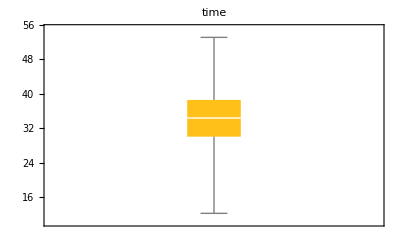

```mathematica
BoxWhiskerChart[time, PlotLabel->"time"]
```

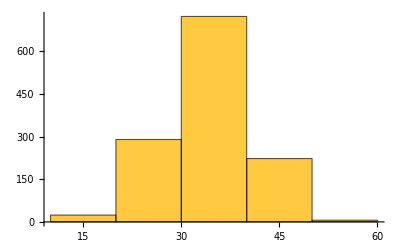

```mathematica
Histogram[time,{10}]
```

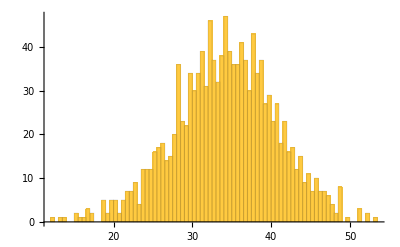

```mathematica
Histogram[time,100]
```

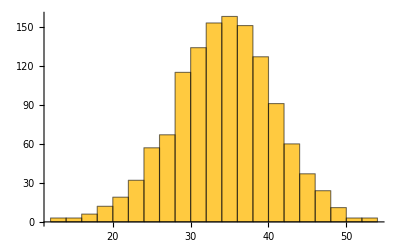

```mathematica
Histogram[time]
```

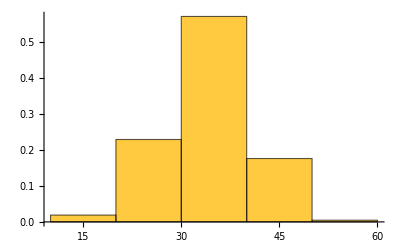

```mathematica
Histogram[time,{10}, "Probability"](*Relative Frequency*)
```

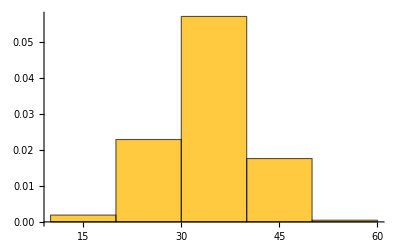

```mathematica
Histogram[time,{10}, "PDF"](*Relative Density*)
```

```mathematica
(*Temp*)
```

```mathematica
Length@temp
```

```mathematica
1266/2
```

633

```mathematica
(Sort[temp][[633]]+Sort[temp][[634]])/2
```

62.9267

```mathematica
{Quartiles[Normal@temp][[1]],Quartiles[Normal@temp][[3]]}
```

{58.2404,67.2389}

```mathematica
{Mean@temp,Median@temp,Min@temp,Max@temp}
```

{62.8639,62.9267,41.7587,87.5824}

```mathematica
Quantile[temp,0.99]
```

80.0342

```mathematica
MeanDeviation@temp
```

5.47386

```mathematica
stdTemp = Standardize@temp;
```

```mathematica
Mean@stdTemp//Chop
```

0

```mathematica
Variance@stdTemp
```

1.

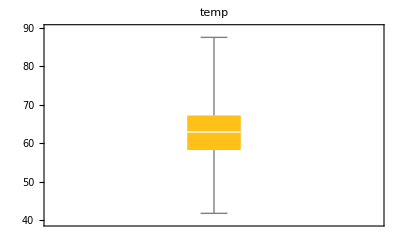

```mathematica
BoxWhiskerChart[temp, PlotLabel->"temp"]
```

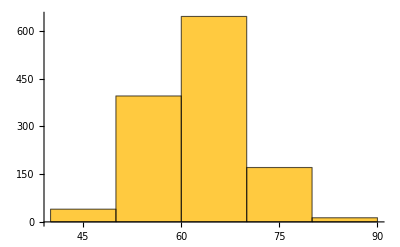

```mathematica
Histogram[temp,{10}]
```

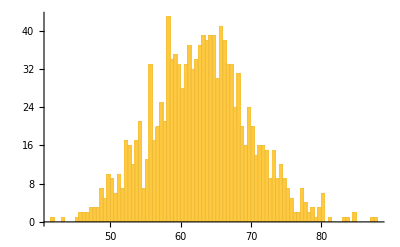

```mathematica
Histogram[temp,100]
```

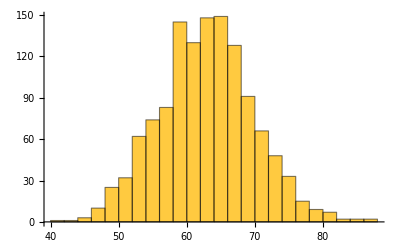

```mathematica
Histogram[temp]
```

```mathematica
domTime = Select[pizzaData, #[[6]]=="Domenico"&][[All,3]];
```

```mathematica
marTime = Select[pizzaData, #[[6]]=="Mario"&][[All,3]];
```

```mathematica
luiTime = Select[pizzaData, #[[6]]=="Luigi"&][[All,3]];
```

```mathematica
salvTime = Select[pizzaData, #[[6]]=="Salvatore"&][[All,3]];
```

```mathematica
brunTime = Select[pizzaData, #[[6]]=="Bruno"&][[All,3]];
```